```mathematica
$Assumptions=var>0&&var1>0&&var2>0;
```

```mathematica
KullbackLeibler[μ1_,var1_,μ2_,var2_]:=Log[var2/var1]/2+(var1+(μ1-μ2)^2)/(2*var2)-1/2;
```

```mathematica
Bhattacharyya[μ1_,var1_,μ2_,var2_]:=(
Log[(var1/var2+var2/var1+2)/4]
+((μ1-μ2)^2/(var1+var2))/4
)/4
```

```mathematica
Hellinger[μ1_,var1_,μ2_,var2_]:=Sqrt[1-Exp[-Bhattacharyya[μ1,var1,μ2,var2]]]
```

## Test special values

```mathematica
KullbackLeibler[μ,var,μ,var]
Bhattacharyya[μ,var,μ,var]
Hellinger[μ,var,μ,var]
```

0

0

0

```mathematica
Limit[KullbackLeibler[0,1,x,1],x->∞]
Limit[Bhattacharyya[0,1,x,1],x->∞]
Limit[Hellinger[0,1,x,1],x->∞]
```

∞

∞

1

## Plot values

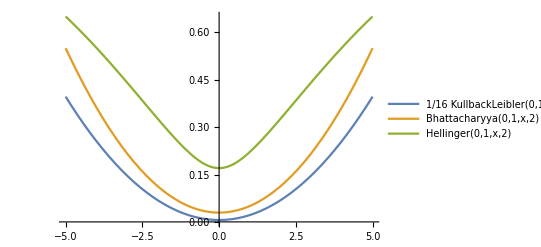

```mathematica
Plot[{KullbackLeibler[0,1,x,2]/16,Bhattacharyya[0,1,x,2],Hellinger[0,1,x,2]},{x,-5,5},PlotLegends->Placed["Expressions",Below]]
```

## Test specific values

```mathematica
KullbackLeibler[0,1,1,2.]
Bhattacharyya[0,1,1,2.]
Hellinger[0,1,1,2.]
```

0.346574

0.0502791

0.221441

```mathematica
pdf[μ_,var_,x_]:=PDF[NormalDistribution[μ,Sqrt[var]],x];
```

```mathematica
overlap=NIntegrate[Min[pdf[0,1,x],pdf[1,2,x]],{x,-∞,∞}]
```

0.65436

```mathematica
bc=NIntegrate[Sqrt[pdf[0,1,x]*pdf[1,2,x]],{x,-∞,∞}]
-Log[bc]
```

0.893348

0.112779